```mathematica
Clear["Global`*"]
```

```mathematica
(*ω0=1;
kp=1;*)
```

```mathematica
Kmat[n_,k1_,k2_]:=ToeplitzMatrix[PadRight[{2k1,-k1},n]]+DiagonalMatrix@Flatten@{-k1+k2,Table[0,n-1]};
V[n_,k2_]:=Flatten@{-k2,Table[0,n-1]};
```

```mathematica
diag[n_,k1_,k2_]:=Module[{m,vals,vecs,T,O},
{vals,O}=Eigensystem[1.*Kmat[n,k1,k2]];
(*m=Norm[O.V[n,k2]]*√n;*)
m=√n;
T=1/m O.V[n,k2];
{vals,T}
]
```

```mathematica
analyticEigval[n_]:=Table[2+2Cos[(k π)/(100+1)],{k,1,n}]
```

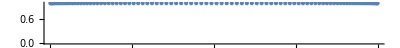

```mathematica
NumberLinePlot@analyticEigval[100]
```

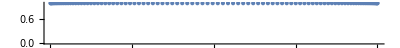

```mathematica
NumberLinePlot@diag[100,1,2][[1]]
```

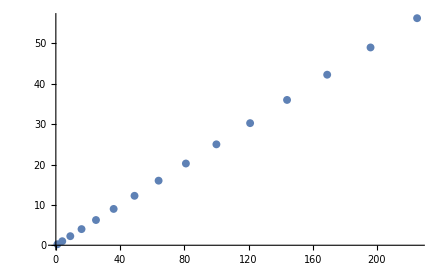

```mathematica
meanT[n_]:=Norm@diag[n,1,2][[2]];
nlist=Range[15]^2;
Tlist=meanT/@nlist;
ListPlot[{nlist,1/Tlist^2}//Transpose]
```

## Response function directly from the sum of the poles

```mathematica
poleEqn[n_,η_,k2_]:=Module[{k1=1,k=4,ω02,M=1,sum,ωα2,T,eqn},
{ωα2,T}=diag[n,k1,k2];
ω02=(k+k2)/M;
sum=Sum[T[[α]]^2/(-z^2+ωα2[[α]]),{α,1,n}];
eqn[ω_]:=Evaluate[(-z^2+ω02-1/M sum)/.z->(ω+I η)];
eqn
]
polePlot[n_,η_]:=ComplexListPlot[ω/.NSolve[poleEqn[n,η,2][ω]==0.,ω],PlotRange->{{-2.5,2.5},{-1,1}}]
```

```mathematica
Manipulate[
polePlot[n,η],{n,5,40,1},{{η,0.1},0,0.3}]
```

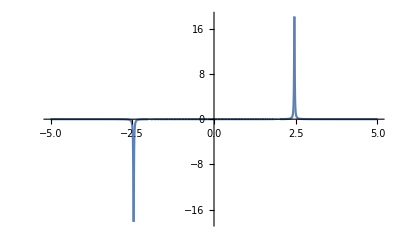

```mathematica
Plot[Im[1/poleEqn[30,0.01,2][ω]],{ω,-5,5},PlotRange->All]
```

```mathematica
Lorenz[x_,Γ_]:=1/π*(Γ/2)/((x)^2+(Γ/2)^2);
Ndist[n_,Γ_]:=Module[{k1=1,k2=2,k=4,ω02,M=1,sum,ωα2,T,eqn,ρ},
{ωα2,T}=diag[n,k1,k2];
ω02=(k+k2)/M;
ρ[Ω2_]:=1/M Sum[T[[α]]^2 Lorenz[Ω2-ωα2[[α]],Γ],{α,1,n}];
ρ
]
```

```mathematica
Manipulate[
Plot[Ndist[n,Γ][ω2],{ω2,0,5},PlotRange->All],{n,5,40,1},{Γ,0.001,0.5}]
```

```mathematica
γgen[n_]:=Module[{Γ,ndist,γp,γpp,γ},
Γ=4/n*3;
ndist=Ndist[n,Γ];
γp[ω_]:=1/ω π*ndist[ω^2](HeavisideTheta[ω]-HeavisideTheta[-ω]);
(*γpp[ω_]:=-1/ωIntegrate[ndist[Ω^2]*(1/(ω+Ω)-1/(ω-Ω)),{Ω,0,∞},PrincipalValue->True];
γ[ω_]:=γp[ω]+I γpp[ω];*)
γp
]
analyticpoleEqn2[n_,ω_]:=(-(ω)^2+6-I (ω) γgen[40][Re@ω])
```

```mathematica
analyticpoleEqn[n_,η_,k2_]:=Module[{k1=1,k=4,ω02,M=1,sum,ωα2,T,eqn,Γ,ndist},
{ωα2,T}=diag[n,k1,k2];
ω02=(k+k2)/M;
Γ=4/n*3;
(*Γ=0.5;*)
ndist=Ndist[n,Γ];
sum[ω_]:=NIntegrate[ndist[Ω^2]/(-(ω+I η)^2+Ω^2)*2Ω,{Ω,0,∞}];
eqn[ω_]:=-(ω+I η)^2+ω02-1/M sum[ω];
eqn
]
```

# Contours of Response function

```mathematica
contour[n_,η_,k2_]:=Module[{p1,p2},
p1=ContourPlot[Abs@poleEqn[n,η,k2][x+I y],{x,-4,4},{y,-1,1},Contours->40,GridLines->{None,{0}},GridLinesStyle->Red,ImageSize->Large];
p2=Plot[{Im[1/(poleEqn[n,η,k2][ω])],Im[1/(analyticpoleEqn[n,η,k2][ω])],Im[1/(-(ω+I*η)^2+6)]},{ω,-4,4},PlotRange->{All,{-1,1}},PlotStyle->{Thick,Dashed,Dashed},ImageSize->Large];
GraphicsRow[{p1,p2},ImageSize->Large]
]
```

```mathematica
Manipulate[
contour[n,η,k2]
,{{n,5},5,30,1},{{η,0.1},0,0.5},{{k2,2},0,5}
]
```

```mathematica
contour[5,0.02,2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ω near {Ω} = {3.97126}. NIntegrate obtained -0.0558956-0.00642698 ⅈ and 6.2096×10^-6 for the integral and error estimates.

-Graphics-

```mathematica
contour[5,0.05,2]
```

-Graphics-

```mathematica
contour[5,0.1,2]
```

-Graphics-

```mathematica
contour[10,0.05,2]
```

-Graphics-

```mathematica
contour[10,0.1,5]
```

-Graphics-

```mathematica
contour[20,0.1,5]
```

-Graphics-

```mathematica
contour[20,0.2,8]
```

-Graphics-

```mathematica
contour[100,0.2,8]
```

-Graphics-